```mathematica
(*Calculations for Proposition A.1 in ``Density Hajnal-Szemeredi theorem for cliques of size four''*)
```

```mathematica
(*Define the function f(b,x2,...,x10), which corresponds to \eta(b,x2,...,x10)*)
f[y_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]:=-(3 x2^2)/112-(3 x3^2)/56-(3 x4^2)/32-x5^2/8-3/8(x6+x7+x8+x9+x10)^2-3/4((x2+x3+x4+x5)x10+(x3+x4+x5)x9+(x4+x5)x8+x5 x7)+y/10 x2+(2y)/10 x3+(3y)/10 x4+(4y)/10 x5+(5y)/10 x6+(6y)/10 x7+(7y)/10 x8+(8y)/10 x9+(9y)/10 x10;
(*Find the maxmimum of f(y,0,0,0,0,0,0,0,0,x10).*)
Expand[Simplify[MaxValue[{f[y,0,0,0,0,0,0,0,0,x10],y>=0&&x10>=0&&x10<=x&&x>=0},{x10}]]]
(*Find the maxmimum of f(y,x2,0,0,0,0,0,0,x9,0).*)
Expand[Simplify[MaxValue[{f[y,x2,0,0,0,0,0,0,x9,0],y>=0&&x2>=0&&x9>=0&&x2+x9<=x&&x>=0},{x2,x9}]]]
(*Find the maxmimum of f(y,x2,x3,0,0,0,0,x8,0,0).*)
Expand[Simplify[MaxValue[{f[y,x2,x3,0,0,0,0,x8,0,0],y>=0&&x2>=0&&x3>=0&&x8>=0&&x2+x3+x8<=x&&x>=0},{x2,x3,x8}]]]
(*Find the maxmimum of f(y,x2,x3,x4,0,0,x7,0,0,0).*)
Expand[Simplify[MaxValue[{f[y,x2,x3,x4,0,0,x7,0,0,0],y>=0&&x2>=0&&x3>=0&&x4>=0&&x7>=0&&x2+x3+x4+x7<=x&&x>=0},{x2,x3,x4,x7}]]]
(*Find the maxmimum of f(y,x2,x3,x4,x5,x6,0,0,0,0).*)
Expand[Simplify[MaxValue[{f[y,x2,x3,x4,x5,x6,0,0,0,0],y>=0&&x2>=0&&x3>=0&&x4>=0&&x5>=0&&x6>=0&&x2+x3+x4+x5+x6<=x&&x>=0},{x2,x3,x4,x5,x6}]]]
```

Piecewise[{{(27 y^2)/50, 5 x≥6 y&&y≥0}, {-(3 x^2)/8+(9 x y)/10, x≥0&&5 x≤6 y}, {-∞, True}}]

Piecewise[{{(13 y^2)/25, 15 x≥44 y&&y≥0}, {-(3 x^2)/8+(4 x y)/5, x≥0&&15 x≤14 y}, {-x^2/40+(11 x y)/75+(343 y^2)/1125, 15 x≥14 y&&15 x≤44 y}, {-∞, True}}]

Piecewise[{{(91 y^2)/150, 3 x≥14 y&&y≥0}, {-(3 x^2)/8+(7 x y)/10, x≥0&&3 x≤2 y}, {-(3 x^2)/64+(21 x y)/80+(7 y^2)/48, 3 x≥2 y&&15 x≤26 y}, {-(3 x^2)/176+(7 x y)/44+(259 y^2)/1100, 15 x≥26 y&&3 x≤14 y}, {-∞, True}}]

Piecewise[{{(19 y^2)/25, 15 x≥92 y&&y≥0}, {-(3 x^2)/8+(3 x y)/5, x≥0&&5 x≤2 y}, {-(3 x^2)/40+(9 x y)/25+(6 y^2)/125, 5 x≥2 y&&15 x≤16 y}, {-x^2/32+(4 x y)/15+(22 y^2)/225, 15 x≥16 y&&3 x≤8 y}, {-(3 x^2)/208+(23 x y)/130+(212 y^2)/975, 3 x≥8 y&&15 x≤92 y}, {-∞, True}}]

Piecewise[{{(151 y^2)/150, 5 x≥38 y&&y≥0}, {-(3 x^2)/8+(x y)/2, x≥0&&15 x≤2 y}, {-(3 x^2)/32+(17 x y)/40+y^2/200, 15 x≥2 y&&3 x≤2 y}, {-(3 x^2)/64+(29 x y)/80+(31 y^2)/1200, 3 x≥2 y&&15 x≤26 y}, {-x^2/40+(43 x y)/150+(103 y^2)/1125, 15 x≥26 y&&15 x≤56 y}, {-(3 x^2)/232+(57 x y)/290+(113 y^2)/435, 15 x≥56 y&&5 x≤38 y}, {-∞, True}}]

```mathematica
(*We compare the five piecewise functions. We may assume y \neq 0. So Let x-axis be x/y and y-axis be max{f}/y^2. We define the following five piecewise functions.*)
```

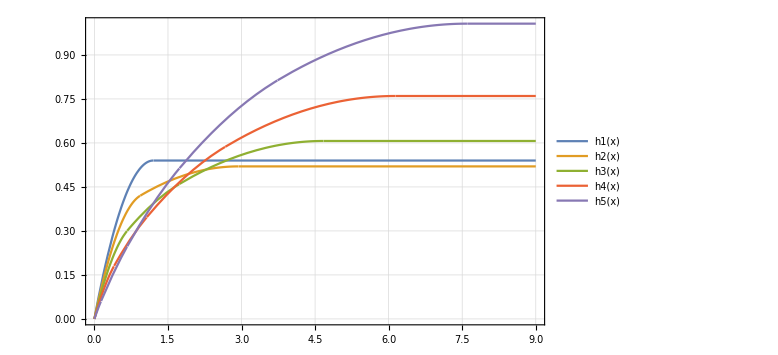

```mathematica
h1[x_]:=Piecewise[{{-(3 x^2)/8+(9 x)/10,x>=0&&x<=6/5},{27/50,x>=6/5}}];
h2[x_]:=Piecewise[{{-(3 x^2)/8+(4 x)/5,x>=0&&x<=14/15},{-x^2/40+(11 x)/75+343/1125,x>=14/15&&x<=44/15},{13/25,x>=44/15}}];
h3[x_]:=Piecewise[{{-(3 x^2)/8+(7 x)/10,x>=0&&x<=2/3},{-(3 x^2)/64+(21 x)/80+7/48,x>=2/3&&x<=26/15},{-(3 x^2)/176+(7 x)/44+259/1100,x>=26/15&&x<=14/3},{91/150,x>=14/3}}];
h4[x_]:=Piecewise[{{-(3 x^2)/8+(3 x)/5,x>=0&&x<=2/5},{-(3 x^2)/40+(9 x)/25+6/125,x>=2/5&&x<=16/15},{-x^2/32+(4 x)/15+22/225,x>=16/15&&x<=8/3},{-(3 x^2)/208+(23 x)/130+212/975,x>=8/3&&x<=92/15},{19/25,x>=92/15}}];
h5[x_]:=Piecewise[{{-(3 x^2)/8+x/2,x>=0&&x<=2/15},{-(3 x^2)/32+(17 x)/40+1/200,x>=2/15&&x<=2/3},{-(3 x^2)/64+(29 x)/80+31/1200,x>=2/3&&x<=26/15},{-x^2/40+(43 x)/150+103/1125,x>=26/15&&x<=56/15},{-(3 x^2)/232+(57 x)/290+113/435,x>=56/15&&x<=38/5},{151/150,x>=38/5}}];
Show[Plot[{h1[x],h2[x],h3[x],h4[x],h5[x]},{x,0,9},PlotTheme->"Detailed",ImageSize->Large]]
```

```mathematica
Simplify[PiecewiseExpand[Max[{h1[x],h2[x],h3[x],h4[x],h5[x]}],0≤x≤8]]
```

Piecewise[{{27/50, 6/5<x≤86/15-4 √(14/15)}, {151/150, x>38/5}, {-3/40 x (-12+5 x), x≤6/5}, {(824+2580 x-225 x^2)/9000, 86/15-4 √(14/15)<x≤56/15}, {(904+684 x-45 x^2)/3480, True}}]

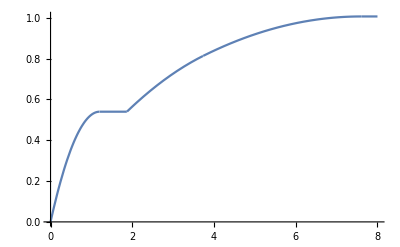

```mathematica
Plot[%17,{x,0,8}]
```